```mathematica
Seminarska naloga


                                                      Računalniška orodja v matematiki
                                                    
                                                                              
                                                                              
                                                                              
                                                                              
                                                                              
                                                                              
                                                                                                  	 Risović Benisa

                                                 
                                                 
                                                 
                                               PREDSTAVITEV FUNKCIJ
                                                 
Linearna funkcija

Linearna funkcija je funkcija, ki jo lahko zapišemo z enačbo oblike f (x) = kx + n, kjer sta koeficienta k in n poljubni realni števili.

Graf linearne funkcije:

Graf linearne funkcije je premica. Ker dve točki natančno določata premico,
lahko graf linearne funkcije narišemo tako, da izračunamo koordinate dveh točk.

Pogosto si pri risanju pomagamo kar s točkama, ki ju določata koeficienta k in n:
Število n pomeni presečišče grafa z ordinatno osjo (f (0) = n). Imenujemo ga odsek na osi y,
ali tudi začetna vrednost.
Število k določa smer premice, zato ga imenujemo smerni koeficient. Ustrezno točko dobimo tako,
da se iz točke N pomaknemo za eno enoto v desno in za k enot navzgor (oziroma navzdol, če je k negativen).
```

```mathematica
Manipulate[Plot[{k*x+n,((-1)/(k))(x-x0)+y0},{x,-5,5},AspectRatio->Automatic,
PlotRange->{-5,5}],{k,-3,3},{n,-3,3},{x0,-3,3},{y0,-3,3}]
```

```mathematica
Eksponentna funkcija

Eksponentna funkcija je matematična funkcija z enačbo oblike f(x) = a^x,
pri čemer je število a pozitivno in različno od 1. Število a imenujemo osnova ali baza eksponentne funkcije.

Eksponentna funkcija, ki ima za osnovo Eulerjevo število e ≈ 2.718 281 828 se imenuje naravna eksponentna funkcija: f(x) = ex.
To funkcijo se včasih zapiše tudi kot: f(x) = exp x

Eksponentna funkcija kot realna funkcija realne spremenljivke ima naslednje lastnosti : 

- Vrednost funkcije je vedno pozitivna - funkcija je navzdol omejena z 0.
- Eksponentna funkcija je navzgor neomejena.
- Če je osnova a večja od 1, funkcija narašča.
- Če je osnova a med 0 in 1, funkcija pada.
```

```mathematica
Plot3D[2^x,{x,-5,5},{y,-5,5},PlotStyle->RGBColor[0.98,0.72,1.]]
```

-Graphics3D-

```mathematica
Logaritemska funkcija

Logaritemska funkcija je inverz eksponentne funkcije.
Logaritem števila b pri osnovi a je tisti eksponent x, za katerega velja ax = b, torej : loga b = x ⇔ ax = b

Zato da x res obstaja, mora biti osnova a pozitivna in različna od 1, logaritmand b pa mora biti pozitiven.
V praksi najpogosteje srečamo logaritem z osnovo 10, ki ga imenujemo tudi desetiški logaritem.
Pri tem logaritmu lahko indeks tudi izpustimo, torej : Subscript[log, 10] b  = log b.
Pogosto srečamo tudi naravni logaritem, ki ima za osnovo Eulerjevo število e = 2.71828 ... Označimo ga : Subscript[log, e] b = ln b.


Lastnosti logaritmov:

Za poljubna pozitivna števila x, y, a, c (a != 1, c != 1) veljajo naslednje lastnosti :

 Subscript[log, a]a = 1

 Subscript[log, a]1= 0

Subscript[log, a] (a^x) = x

Subscript[log, a] (xy) = Subscript[log, a]x + Subscript[log, a]y

Subscript[log, a] (x/y) =  Subscript[log, a]x - Subscript[log, a]y

Subscript[log, a] (x^n) = n Subscript[log, a] (x)
 
Subscript[log, a] (x^(1/n)) = 1/nSubscript[log, a]x

Subscript[log, c] x = (Subscript[log, a] x)/(Subscript[log, a] c)


Graf logaritemske funkcije

Logaritemska funkcija f (x) =  Subscript[log, a]x mora imeti osnovo pozitivno in različno od 1.
```

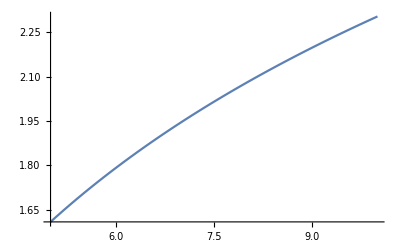

```mathematica
Plot[Log[x], {x,5, 10}]
```

```mathematica
Trigonometricne funkcije:

 sin(x)
 
Df = R
Zf = [−1, 1]
Ničle: x = kπ ;   k ∈ Z
Maksimumi: M(π/2 + 2kπ, 1) ;   k ∈ Z
Minimumi: m(−π/2 + 2kπ, −1) ;   k ∈ Z
```

```mathematica
Plot3D[Sin[x],{x,-10,10},{y,-1,1},PlotStyle->RGBColor[1.,0.56,0.89]]
```

-Graphics3D-

```mathematica
Manipulate[Plot[a *Sin[k*x+n],{x,-5,5},PlotRange->{-5,5},AspectRatio->Automatic],{a,-3,3},{k,-3,3},{n,-3,3}]
```

```mathematica
cos(x)

Df = R
Zf = [−1, 1]
Ničle: x =π /2 + kπ ;   k ∈ Z
Maksimumi: M(2kπ, 1) ;   k ∈ Z
Minimumi: m(π + 2kπ, −1) ;   k ∈ Z
```

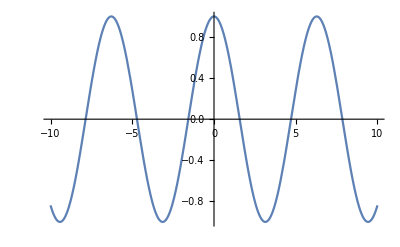

```mathematica
Plot[Cos[x],{x,-10,10}]
```

```mathematica
Manipulate[Plot3D[a*Cos[k*x + n],{x,-5,5},{y,-5,5},PlotStyle->RGBColor[1.,0.56,0.89], ImageSize->Large], {a,-3,3},{k,-3,3},{n,-3,3}]
```

```mathematica
tan(x)
Df = R \ {π/2 + kπ ;  k ∈ Z}
Zf = R
Ničle: x = kπ ;   k ∈ Z
Poli: x = π/2 + kπ ;   k ∈ Z
```

```mathematica
Plot3D[Tan[x],{x,-10,10},{y,-10,10},PlotStyle->RGBColor[1.,0.56,0.89], ImageSize->Large]
```

-Graphics3D-

```mathematica
Graficno resevanje matematicnih problemov:

1.Določi tangento na funkcijo y = sin^2 x - cos x , v točki (2,y(2)). Rezultat predstavi s sliko.
```

```mathematica
y[x_]:=(Sin[x])^2-Cos[x]
```

```mathematica
odvod=D[y[x],x]
```

```mathematica
Sin[x]+2 Cos[x] Sin[x]
```

```mathematica
k=odvod/.{x->2}
```

```mathematica
Sin[2]+2 Cos[2] Sin[2]
```

```mathematica
x0=2
```

```mathematica
2
```

```mathematica
y0=y[x]/.x->2
```

```mathematica
-Cos[2]+Sin[2]^2
```

```mathematica
t=k*(x-x0)+y0
```

```mathematica
-Cos[2]+Sin[2]^2+(-2+x) (Sin[2]+2 Cos[2] Sin[2])
```

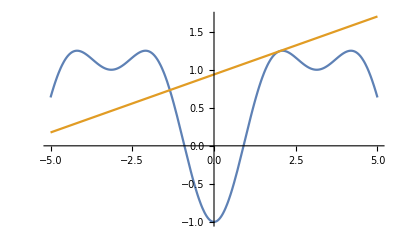

```mathematica
Plot[{y[x],t},{x,-5,5}]
```

```mathematica
2. Dana je parametrično podana krivulja (((3-t) sin t)/(1+t),cos(t) sin(2 t)) za t ∈ [0,5]. Krivulja samo sebe preseka natanko dvakrat.
Rezultat prikaži s sliko, ki jo predela ukaz ParametricPlot.
```

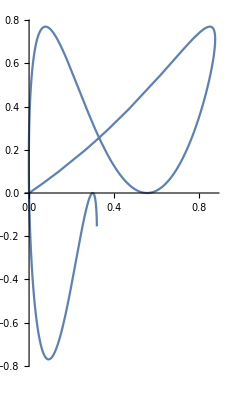

```mathematica
ParametricPlot[{((3-t)*Sin[t])/(1+t),Cos[t]*Sin[2*t]},{t,0,5}]
```

3.Določi inverzno funkcijo funkcije f(x) = x^-1+ 2 ter nariši grafa obeh funkcij v istem koordinatnem sistemu.

```mathematica
Solve[1/y+2==x,{y}]
```

{{y→1/(-2+x)}}

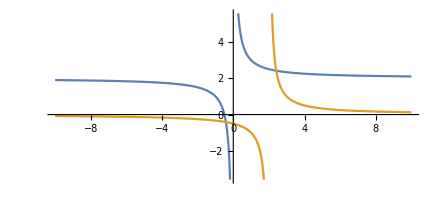

```mathematica
Plot[{1/x +2,1/(x-2)},{x,-10,10},AspectRatio->Automatic]
```